```mathematica
i=ImageResize[-Graphics-,500];
```

```mathematica
logogramDirectory=FileNameJoin[{NotebookDirectory[],"ScriptLogoJpegs"}];
```

```mathematica
i2=(ImageResize[#,500]&)/@Import/@(FileNameJoin[{logogramDirectory,#}]&)/@Select[StringMatchQ[#,___~~".jpg"]&]@Import@logogramDirectory;
```

```mathematica
i2[[1;;2]]
```

{-Graphics-,-Graphics-}

```mathematica
i2[[7;;8]]
```

{-Graphics-,-Graphics-}

```mathematica
ColorNegate@ImageDifference[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
ColorNegate@ImageDifference[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
ColorNegate@ImageDifference[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
fef=FeatureExtraction[i2,"ImageFeatures"]
```

```mathematica
fef=FeatureExtraction[i2]
```

FeatureExtractorFunction[…]

```mathematica
fef[-Graphics-]
```

{0.0777689,0.680716,-2.09869,0.78388,5.92825,6.17203,-1.14096,5.16148,-2.31,4.29076,-2.2228,3.65909,-2.85907,6.80296,-5.79111,-4.06718,2.34577,2.96437,2.99737,-1.93189,0.252624,4.03886,2.8112,-2.12023,6.38333,-3.48772,3.96112,-2.47747,0.970497,-4.32015,0.798684,3.52928,-0.517095,-1.5944,-3.05156,7.34973,3.94024}

```mathematica
featureVectors=fef[i2];
```

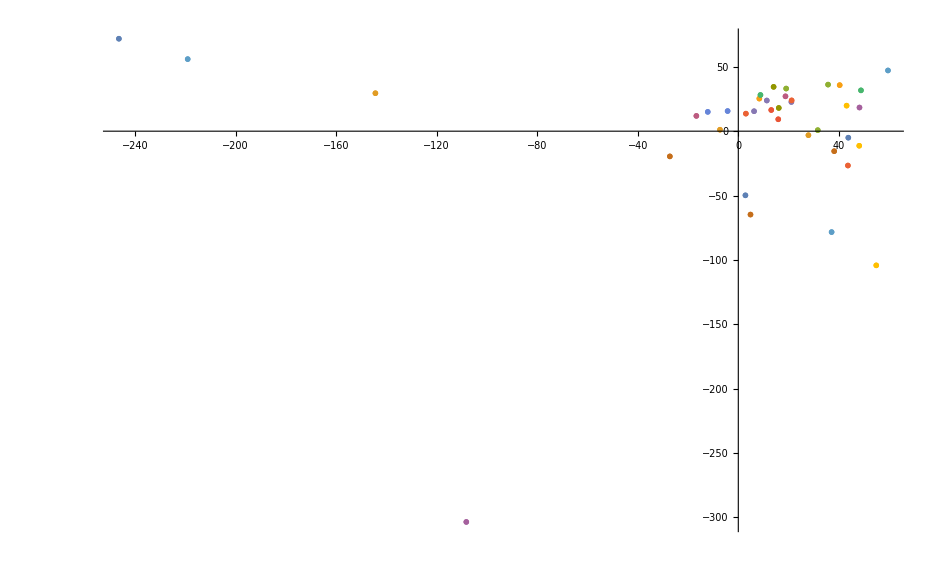

```mathematica
ListPlot[List/@DimensionReduce[featureVectors,2,Method->"LatentSemanticAnalysis"],PlotMarkers->(Show[SetAlphaChannel[#,ColorNegate@#],ImageSize->50]&/@i2),PlotRange->All]
```

```mathematica
ClusteringTree[featureVectors->(Show[SetAlphaChannel[#,ColorNegate@#],ImageSize->40]&/@i2),ClusterDissimilarityFunction->"Complete"]
```

-Graphics-

```mathematica
ClusteringTree[featureVectors->(Show[SetAlphaChannel[#,ColorNegate@#],ImageSize->40]&/@i2),ClusterDissimilarityFunction->"Average"]
```

-Graphics-

```mathematica
alignedDifference[img1_,img2_]:=ImageDifference[img1,ImageAlign[img1,img2,Background->White]]
```

```mathematica
alignedDifference[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
i2=ColorConvert[i2,"Grayscale"];
```

```mathematica
nf=Nearest[i2,DistanceFunction->(ImageMeasurements[alignedDifference[#1,#2],"Mean"]&)]
```

NearestFunction[{1, <>}]

Will take about 2 hours (on Chris’s computer)

```mathematica
alignedDifference[#,nf[#,2][[2]]]&/@i2[[;;15]]
```

$Aborted

```mathematica
alignedDifference[#,nf[#,2][[2]]]&@i2[[2]]
```

-Graphics-

FeatureNearest is only available in 11.1

```mathematica
fnf=FeatureNearest[i2,FeatureExtractor->"ImageFeatures"]
```

NearestFunction[…]

```mathematica
fnf=FeatureNearest[i2]
```

NearestFunction[…]

```mathematica
alignedDifference[#,fnf[#,2][[2]]]&@i2[[7]]
```

-Graphics-

```mathematica
alignedDifference[#,fnf[#,2][[2]]]&/@i2
```

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageMultiply@@i2
```

-Graphics-

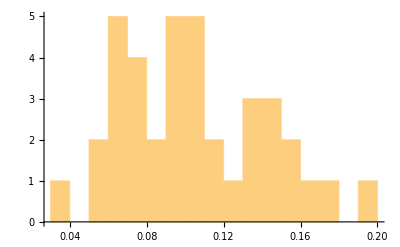

```mathematica
Histogram[ImageMeasurements[ColorNegate/@i2,"Mean"],{0.01}]
```

```mathematica
Mean@ImageMeasurements[ColorNegate/@i2,"Mean"]
```

0.104121

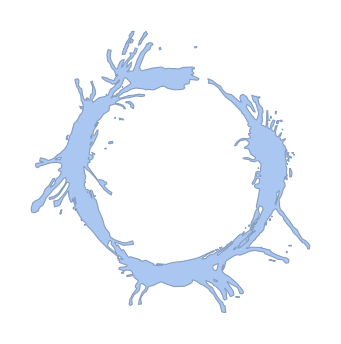

```mathematica
ImageMesh[ColorNegate@i]
```

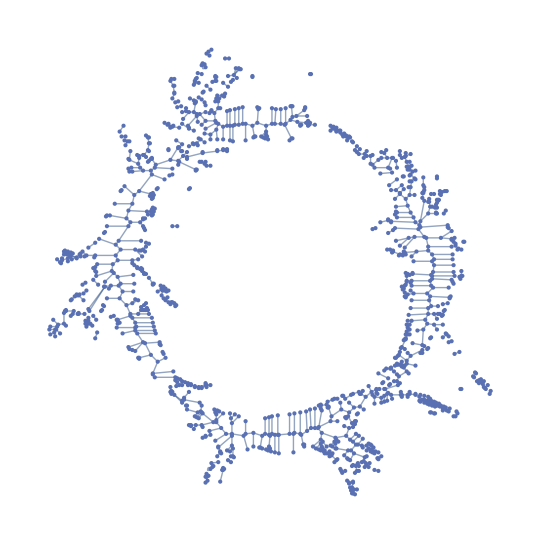

```mathematica
MorphologicalGraph[ColorNegate@i]
```